```mathematica
f[r_,Q_,l_]:= 1 - ((2*r-Q^2)*r^2)/(r^4+(2*r+Q^2)l^2);
ll=Table[l,{l,0.01,0.77,0.001}];
```

```mathematica
QQ=Table[Q/.FindRoot[{(f[r,Q,l]/.{l->ll[[i]]})==0,D[(f[r,Q,l]/.{l->ll[[i]]}),r]==0},{{r,1},{Q,1}}],{i,1,Length[ll]}];
QQll=Table[{QQ[[i]],ll[[i]]},{i,1,Length[ll]}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

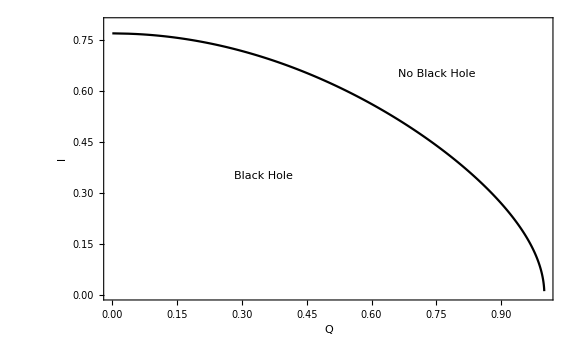

```mathematica
ListLinePlot[QQll,Frame->True,FrameLabel->{"Q","l"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,FontColor->Black],PlotStyle->Black,PlotRange->{{0.,1},{0,0.8}},BaseStyle->{14,FontFamily->"TimesNewRoman"},
Epilog->{Text[Rotate[Framed["Black Hole",FrameStyle->None,Background->None],0Degree],{0.35,0.35}],Text[Rotate[Framed["No Black Hole",FrameStyle->None,Background->None],0Degree],{0.75,0.65}]},ImageSize->Large]
```

```mathematica
Q/.FindRoot[{(f[r,Q,l]/.{l->0.769})==0,D[(f[r,Q,l]/.{l->0.769}),r]==0},{{r,1},{Q,1}}]
```

0.0372333

```mathematica
BaseStyle->{14,FontFamily->"TimesNewRoman"},
Epilog->{Text[Rotate[Framed["Black Hole",FrameStyle->None,Background->None],0Degree],{0.25,0.25}],Text[Rotate[Framed["No Black Hole",FrameStyle->None,Background->None],0Degree],{0.75,0.55}]}
```

```mathematica
Vef[r_, Q_,l_,M_,Ene_,L_] := -Ene^2(-1+((2M r-Q^2)r^2)/(r^4 +(2M r+Q^2)l^2))^-1- L^2/r^2;
Solve[Vef[r,Q,l,M,Ene,L]==0,Ene]//Simplify
```

{{Ene→-(L √((1+2 r+r^2-2 r^3+r^4)/(1+2 r+r^4)))/r},{Ene→(L √((1+2 r+r^2-2 r^3+r^4)/(1+2 r+r^4)))/r}}

```mathematica
D[Vef[r,Q,l,M,Ene,L],r]/.Ene->-(L √((l^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r)))/(r^4+l^2 (Q^2+2 M r))))/r //Simplify
```

(2 L^2 (1+4 r+4 r^2+2 r^3+2 r^4+4 r^5+2 r^6-3 r^7+r^8))/(r^3 (1+2 r+r^4) (1+2 r+r^2-2 r^3+r^4))

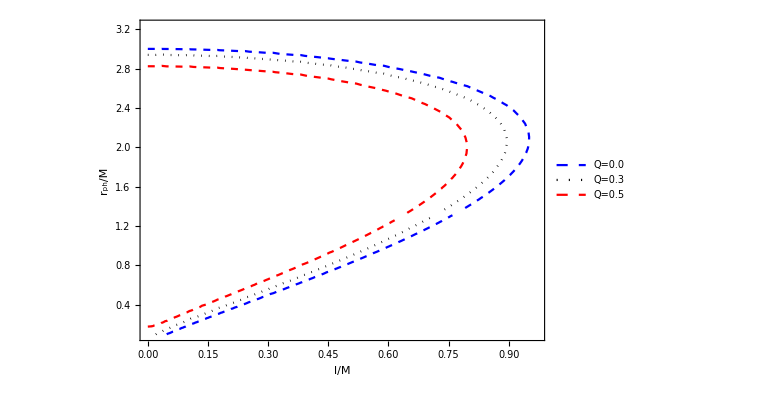

```mathematica
k[l_,Q_,M_,r_,L_]:=(2 L^2(l^4 (Q^2+2 M r)^2+r^6 (2 Q^2+r (-3 M+r))+2 l^2 r^3 (Q^2 r+M (Q^2+2 r^2))))/(r^3 (r^4+l^2 (Q^2+2 M r)) (l^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r))))
M=1;
ContourPlot[{k[l,0.0,M,r]==0,k[l,0.3,M,r]==0,k[l,0.5,M,r]==0},{l,0.00,0.97},{r,0.1,3.23},PlotLegends->Placed[{"Q=0.0","Q=0.3","Q=0.5"},{Scaled[{0.715,0.16}],{0,0.5}}],ContourStyle->{{Dashed,Blue},{Dotted,Black},{Dashed,Red},{Dashed,Yellow},{Dashed,Green}},FrameLabel->{" l/M","r_ph/M"},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large]
```

```mathematica
(* BAXTIYOR AKA l PARAMETR CHEGARASINI 0.97 QILDIM AMMO 0.769 DAN BOSHLAB NO BLACK HOLE region bolyapti ? ? ? *)
```

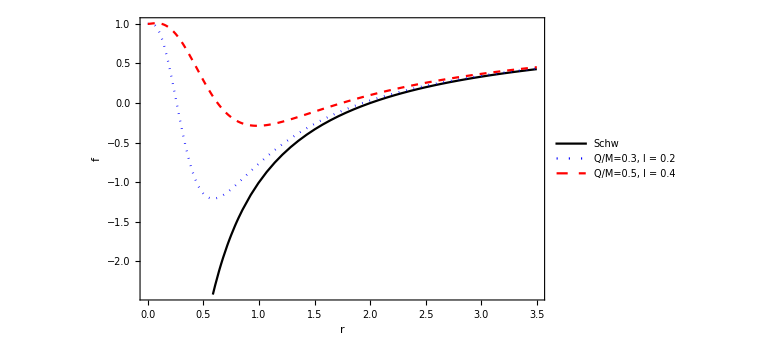

```mathematica
Plot[{f[r,0,0],f[r,0.3,0.2],f[r,0.5,0.4]},{r,0.,3.5},PlotStyle->{{Black},{Dotted,Blue},{Dashed,Red}},FrameLabel->{"r","f"},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large, PlotLegends->Placed[{"Schw","Q/M=0.3, l = 0.2","Q/M=0.5, l = 0.4"},Scaled[{0.75,0.25}]] ]
```

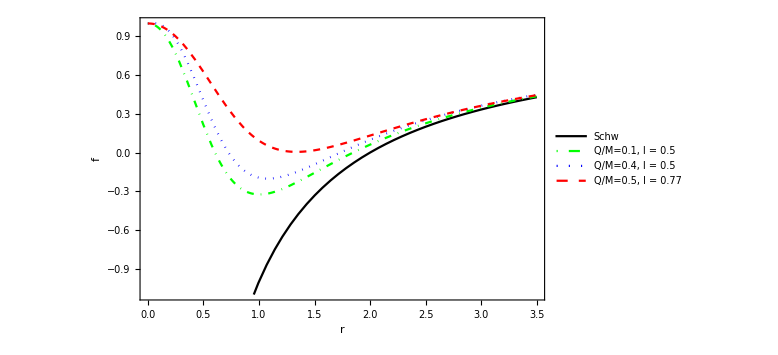

```mathematica
Plot[{f[r,0,0],f[r,0.1,0.5],f[r,0.4,0.5],f[r,0.1,0.77]},{r,0.,3.5},PlotStyle->{{Black},{Green,DotDashed},{Dotted,Blue},{Dashed,Red}},FrameLabel->{"r","f"},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large, PlotLegends->Placed[{"Schw","Q/M=0.1, l = 0.5","Q/M=0.4, l = 0.5","Q/M=0.5, l = 0.77"},Scaled[{0.75,0.25}]] ]
```

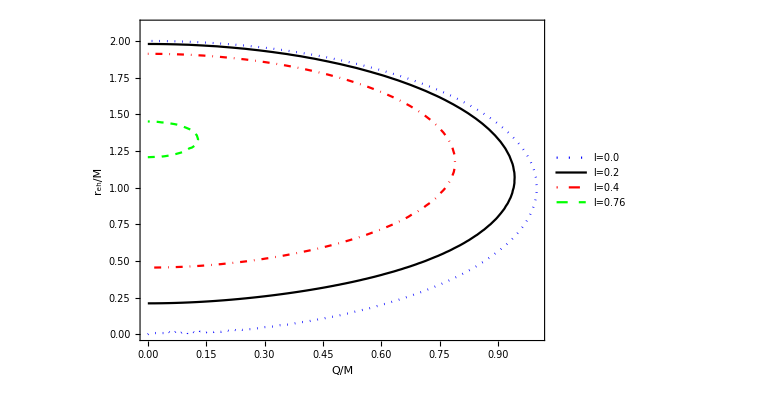

```mathematica
ContourPlot[{f[r,Q,0.0]==0,f[r,Q,0.2]==0,f[r,Q,0.4]==0,f[r,Q,0.76]==0},{Q,0,1},{r,0.0000003(*1/0 nol bolgani uchun*),2.},PlotLegends->Placed[{"l=0.0","l=0.2","l=0.4","l=0.76"},{Scaled[{0.3,0.35}],{0,0.0}}],ContourStyle->{{Dotted,Blue},{Black},{DotDashed,Red},{Dashed,Green},{Dashed,Green}},FrameLabel->{" Q/M","r_eh/M"},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,PlotRange->{ {0,1},{0.,2.1} }]
(*Subscript[r, eh] =NSolve[f[r,Q,l]==0,r,Reals]/.{{Q->0.0},{l->0.4}}*)
```

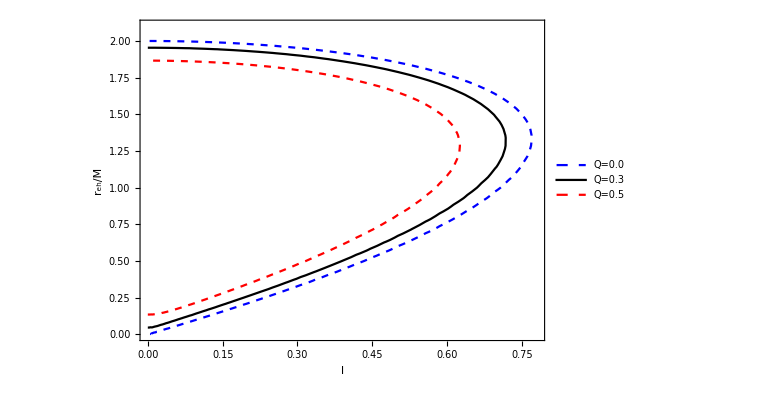

```mathematica
ContourPlot[{f[r,0.0,l]==0,f[r,0.3,l]==0,f[r,0.5,l]==0},{l,0,0.78},{r,0.0000001(*1/0 nol bolgani uchun*),2.},PlotLegends->Placed[{"Q=0.0","Q=0.3","Q=0.5"},{Scaled[{0.77,0.15}],{0,0.5}}],ContourStyle->{{Dashed,Blue},{Black},{Dashed,Red},{Dashed,Yellow},{Dashed,Green}},FrameLabel->{" l","r_eh/M"},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,PlotRange->{ {0,0.78},{0.,2.1} }]
```